```mathematica
Hs[q_,n_,κ_,c_,k0_,k_]:=Sum[(-1)^σ Binomial[κ,σ]k^n Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))Hypergeometric2F1Regularized[(2-q+n)/2,(3-q+n)/2,1+n,-k^2/(σ c - I k0)^2],{σ,0,κ}]
```

```mathematica
c=0.1;
κ=4;
k0=1;
k=3;
NIntegrate[(k0 x)^(-2) Exp[I k0 x] x BesselJ[0, k x] (1-Exp[-c x])^κ,{x,0,∞}]
```

-2.3013×10^-6+5.47542×10^-6 ⅈ

```mathematica
NLimit[ Hs[q,0,4,0.1,1,3],q->2]
```

NLimit[(0.4-1. ⅈ)^(-2+q) Gamma[2-q] Hypergeometric2F1Regularized[(2-q)/2,(3-q)/2,1,5.61831-5.35077 ⅈ]-4 (0.3-1. ⅈ)^(-2+q) Gamma[2-q] Hypergeometric2F1Regularized[(2-q)/2,(3-q)/2,1,6.89336-4.54507 ⅈ]+6 (0.2-1. ⅈ)^(-2+q) Gamma[2-q] Hypergeometric2F1Regularized[(2-q)/2,(3-q)/2,1,7.98817-3.3284 ⅈ]-4 (0.1-1. ⅈ)^(-2+q) Gamma[2-q] Hypergeometric2F1Regularized[(2-q)/2,(3-q)/2,1,8.73444-1.76453 ⅈ]+(0.-1. ⅈ)^(-2+q) Gamma[2-q] Hypergeometric2F1Regularized[(2-q)/2,(3-q)/2,1,9.+0. ⅈ],q→2]

```mathematica
Hs[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs2[q_,n_,κ_,c_,k0_,k_]:=Sum[(-1)^σ Binomial[κ,σ]k^n Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))(
π (k^2/(σ c -I k0)^2)^(-(2-q+n)/2)/Gamma[(3-q+n)/2]/Gamma[1+n-(2-q+n)/2]
  Hypergeometric2F1Regularized[(2-q+n)/2,(2-q-n)/2,1/2,-(σ c-I k0)^2/k^2]
-π (k^2/(σ c -I k0)^2)^(-(3-q+n)/2)/Gamma[(2-q+n)/2]/Gamma[1+n-(3-q+n)/2]
  Hypergeometric2F1Regularized[(3-q+n)/2,(3-q-n)/2,3/2,-(σ c-I k0)^2/k^2])
,{σ,0,κ}]
```

```mathematica
Hs2[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs20[q_,n_,κ_,c_,k0_,k_]:=π Sum[(-1)^σ Binomial[κ,σ]k^n Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))(
 (k^2/(σ c -I k0)^2)^(-(2-q+n)/2)/Gamma[(3-q+n)/2]/Gamma[(q+n)/2]
  Hypergeometric2F1Regularized[(2-q+n)/2,(2-q-n)/2,1/2,-(σ c-I k0)^2/k^2]
- (k^2/(σ c -I k0)^2)^(-(3-q+n)/2)/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2]
  Hypergeometric2F1Regularized[(3-q+n)/2,(3-q-n)/2,3/2,-(σ c-I k0)^2/k^2])
,{σ,0,κ}]
```

```mathematica
Hs20[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs3[q_,n_,κ_,c_,k0_,k_]:=Sum[(-1)^σ Binomial[κ,σ]k^(q-2) Gamma[2-q+n]Gamma[1+n]
/(2^n k0^q (σ c - I k0)^(3/2(2-q+n)))
    Pochhammer[(3-q+n)/2,-(2-q+n)/2]/Pochhammer[1+n,-(2-q+n)]
Hypergeometric2F1[(2-q+n)/2,(2-q-n)/2,1/2,-(σ-I k0)^2/k^2]
,{σ,0,κ}]
```

```mathematica
Hs3[2.001,0,4,0.1,1,3]
```

0.000596127-0.000580205 ⅈ

```mathematica
Hs4[q_,n_,κ_,c_,k0_,k_]:=Sum[(-1)^σ Binomial[κ,σ]k^n /Gamma[1+n] Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))Hypergeometric2F1[(2-q+n)/2,(3-q+n)/2,1+n,-k^2/(σ c - I k0)^2],{σ,0,κ}]
```

```mathematica
Hs4[2.001,2,4,0.1,1,3]
```

3.36344×10^-6-8.61366×10^-6 ⅈ

```mathematica
Hs5[q_,n_,κ_,c_,k0_,k_]:=Sum[(-1)^σ Binomial[κ,σ]k^(q-2)  Gamma[2-q+n]/
(2^n k0^q (σ c - I k0)^(3/2(2-q+n)) Gamma[1+n])
Pochhammer[(3-q+n)/2,-(2-q+n)/2]/Pochhammer[1+n,-(2-q+n)/2]
Hypergeometric2F1[(2-q+n)/2,(2-q-n)/2,1/2,-(σ c - I k0)^2/k^2]
,{σ,0,κ}]
```

```mathematica
Hs5[2.000,2,4,0.1,1,3]
```

-0.0139151-0.00305762 ⅈ

```mathematica
Hs6[q_,n_,κ_,c_,k0_,k_]:=Sum[Sum[(-1)^σ Binomial[κ,σ]k^(-2+q-2s)  Gamma[2-q+n]π/
(2^n k0^q )(
    Pochhammer[(2-q+n)/2,s]Pochhammer[(2-q-n)/2,s]
  / (Gamma[(3-q+n)/2]Gamma[(q+n)/2]Gamma[1/2+s] s!)
-Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]
  / (Gamma[(2-q+n)/2]Gamma[(q+n-1)/2]Gamma[3/2+s] s!)
      (-σ c-I k0)/k

)
,{σ,0,κ}],{s,0,∞}]
```

```mathematica
Hs6[2.1,0,4,0.1,1,3]
```

8.84728×10^-15-5.68099×10^-16 ⅈ

```mathematica
Hs21[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ]k^n Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))(
 (k^2/(σ c -I k0)^2)^(-(2-q+n)/2)/Gamma[(3-q+n)/2]/Gamma[(q+n)/2]
  Hypergeometric2F1Regularized[(2-q+n)/2,(2-q-n)/2,1/2,-(σ c-I k0)^2/k^2]
- (k^2/(σ c -I k0)^2)^(-(3-q+n)/2)/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2]
  Hypergeometric2F1Regularized[(3-q+n)/2,(3-q-n)/2,3/2,-(σ c-I k0)^2/k^2])
,{σ,0,κ}]
```

```mathematica
Hs21[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs3a[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ]k^n Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))Sum[
 (k^2/(σ c -I k0)^2)^(-(2-q+n)/2)/Gamma[(3-q+n)/2]/Gamma[(q+n)/2]
 Pochhammer[(2-q+n)/2,s]Pochhammer[(2-q-n)/2,s]/Gamma[1/2+s]/s!
	(-(σ c-I k0)^2/k^2)^s
- (k^2/(σ c -I k0)^2)^(-(3-q+n)/2)/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2]
  Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]/Gamma[3/2+s]/s!
	(-(σ c-I k0)^2/k^2)^s,
{s,0,∞}]
,{σ,0,κ}]
```

```mathematica
Hs3a[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
//otočené pořadí sumy:
```

```mathematica
Hs3b[q_,n_,κ_,c_,k0_,k_]:= π Sum[ Sum[(-1)^σ Binomial[κ,σ]k^n Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))(
 (k^2/(σ c -I k0)^2)^(-(2-q+n)/2)/Gamma[(3-q+n)/2]/Gamma[(q+n)/2]
 Pochhammer[(2-q+n)/2,s]Pochhammer[(2-q-n)/2,s]/Gamma[1/2+s]/s!
	(-(σ c-I k0)^2/k^2)^s
- (k^2/(σ c -I k0)^2)^(-(3-q+n)/2)/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2]
  Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]/Gamma[3/2+s]/s!
	(-(σ c-I k0)^2/k^2)^s
)
,{σ,0,κ}]
,{s,0,∞}]
```

```mathematica
Hs3b[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs4a[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ]k^n Gamma[2-q+n]/(2^n k0^q (σ c - I k0)^(2-q+n))Sum[(-1)^s(
 Pochhammer[(2-q+n)/2,s]Pochhammer[(2-q-n)/2,s]
/Gamma[1/2+s]/s!/Gamma[(3-q+n)/2]/Gamma[(q+n)/2]
k^(-2+q-n-2s)(σ c-I k0)^(2-q+n+2s)
- Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]
/Gamma[3/2+s]/s!/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2]
 k^(-3+q-n-2s)(σ c-I k0)^(3-q+n+2s)
),{s,0,∞}]
,{σ,0,κ}]
```

```mathematica
Hs4a[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs4b[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ] Gamma[2-q+n]/
(2^n k0^q)
Sum[(-1)^s(
 Pochhammer[(2-q+n)/2,s]Pochhammer[(2-q-n)/2,s]
/Gamma[1/2+s]/s!/Gamma[(3-q+n)/2]/Gamma[(q+n)/2]
k^(-2+q-2s)(σ c-I k0)^(2s)
- Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]
/Gamma[3/2+s]/s!/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2]
 k^(-3+q-2s)(σ c-I k0)^(1+2s)
),{s,0,∞}]
,{σ,0,κ}]
```

```mathematica
Hs4b[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs4c[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ] Gamma[2-q+n]/
(2^n k0^q)
Sum[(-1)^s k^(-2+q-2s)(σ c-I k0)^(2s)(
 (Pochhammer[(2-q+n)/2,s]Pochhammer[(2-q-n)/2,s]
/Gamma[1/2+s]/s!/Gamma[(3-q+n)/2]/Gamma[(q+n)/2])
- (Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]
/Gamma[3/2+s]/s!/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2])
 (σ c-I k0)/k
),{s,0,∞}]
,{σ,0,κ}]
```

```mathematica
Hs4c[2.001,0,4,0.1,1,3]
```

-2.31014×10^-6+5.46969×10^-6 ⅈ

```mathematica
Hs4d[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ] Gamma[2-q+n]/
(2^n k0^q)
Sum[(-1)^s k^(-2+q-2s)(σ c-I k0)^(2s)(
 (Pochhammer[(2-q+n)/2,s]Pochhammer[(2-q-n)/2,s]
/Gamma[1/2+s]/s!/Gamma[(3-q+n)/2]/Gamma[(q+n)/2])
- (Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]
/Gamma[3/2+s]/s!/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2])
 (σ c-I k0)/k
),{s,Ceiling[κ/2],∞}]
,{σ,0,κ}]
```

```mathematica
Hs4d[2.00001,0,4,0.1,1,3]
```

-2.30142×10^-6+5.47536×10^-6 ⅈ

```mathematica
Sum[Gamma[s+1/2](-1)^s/(s+1/2)/s!x^s,{s,0,∞}]
```

(2 √π ArcSinh[√x])/(√x)

```mathematica
Gamma[1/2]
```

√π

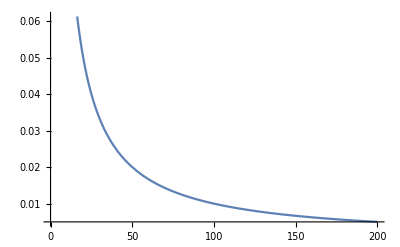

```mathematica
Plot[ArcSinh[1/x],{x,0,200}]
```

```mathematica
HsSq2n0a[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ] Gamma[2-q+n]/
(2^n k0^q)
Sum[(-1)^s k^(-2+q-2s)(σ c-I k0)^(2s)(
- (Pochhammer[(3-q+n)/2,s]Pochhammer[(3-q-n)/2,s]
/Gamma[3/2+s]/s!/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2])
 (σ c-I k0)/k
),{s,Ceiling[κ/2],∞}]
,{σ,0,κ}]
```

```mathematica
HsSq2n0a[2.00001,0,4,0.1,1,3]
```

-2.30128×10^-6+5.47539×10^-6 ⅈ

```mathematica
HsSq2n0b[q_,n_,κ_,c_,k0_,k_]:= π Sum[(-1)^σ Binomial[κ,σ] Gamma[2-q+n]/
(k0^2)
Sum[(-1)^s k^(-2s)(σ c-I k0)^(2s)(
- (Pochhammer[1/2,s]Pochhammer[1/2,s]
/Gamma[3/2+s]/s!/Gamma[(2-q+n)/2]/Gamma[(q+n-1)/2])
 (σ c-I k0)/k
),{s,Ceiling[κ/2],∞}]
,{σ,0,κ}]
```

```mathematica
HsSq2n0b[2.00001,0,4,0.1,1,3]
```

-2.30133×10^-6+5.47549×10^-6 ⅈ

```mathematica
HsSpecq2n0f[κ_,c_,k0_,k_]:=-Sqrt[π]k0^(-2)k^(-2)Sum[(-1)^σ Binomial[κ,σ]

(σ c-I k0)^2 ArcSinh[((σ c-I k0)/k)], {σ,0,κ}]
```

```mathematica
HsSpecq2nf[4,0.1,1,3]
```

7.3313×10^-6-0.0000197585 ⅈ

```mathematica
HsSq2n0c[κ_,c_,k0_,k_]:=-Sum[(-1)^σ Binomial[κ,σ]1/(2k0^2)Sum[(-1)^s k^(-2s-1)(σ c-I k0)^(2s+1)Gamma[1/2+s]/(Sqrt[π](1/2+s)s!),{s,0,∞}],{σ,0,κ}]
```

```mathematica
HsSq2n0c[4,0.1,1,3]
```

-2.3013×10^-6+5.47542×10^-6 ⅈ

```mathematica
HsSq2n0d[κ_,c_,k0_,k_]:=-Sum[(-1)^σ (σ c-I k0)/k Binomial[κ,σ]1/(2k0^2)Sum[(-1)^s ((σ c-I k0)/k)^(2s)Gamma[1/2+s]/(Sqrt[π](1/2+s)s!),{s,0,∞}],{σ,0,κ}]
```

```mathematica
HsSq2n0d[4,0.1,1,3]
```

-2.3013×10^-6+5.47542×10^-6 ⅈ

```mathematica
HsSq2n0e[κ_,c_,k0_,k_]:=-Sum[(-1)^σ Binomial[κ,σ]1/(2k0^2)Sum[(-1)^s ((σ c-I k0)/k)^(2s+1)Gamma[1/2+s]/(Sqrt[π](1/2+s)s!),{s,0,∞}],{σ,0,κ}]
```

```mathematica
HsSq2n0e[4,0.1,1,3]
```

-2.3013×10^-6+5.47542×10^-6 ⅈ

```mathematica
HsSq2n0f[κ_,c_,k0_,k_]:=-Sum[(-1)^σ Binomial[κ,σ]1/k0^2ArcSinh[(σ c-I k0)/k],{σ,0,κ}]
```

```mathematica
HsSq2n0f[4,0.1,1,3]
```

-2.3013×10^-6+5.47542×10^-6 ⅈ

```mathematica
Sum[(-1)^s (x)^(2s+1)Gamma[1/2+s]/(Sqrt[π](1/2+s)s!),{s,0,∞}]
```

2 ArcSinh[x]

```mathematica
Sum[(-1)^s x^(2s+1)Gamma[1/2+s]/(Sqrt[π](1/2+s)s!),{s,0,∞}]
```

2 ArcSinh[x]